```mathematica
foldname="C:\\Users\\msztr\\OneDrive\\Documents\\GitHub\\VeriGudGame\\Measurements\\Iron_Big"
filenms = FileNames[All,foldname];
```

C:\Users\msztr\OneDrive\Documents\GitHub\VeriGudGame\Measurements\Iron_Big

```mathematica
samplerate=125 10^6;
```

```mathematica
res=Table[dat=Import[filenms[[i]]][[5;;-1]];
dat1={#[[1]]/samplerate,#[[2]]}&/@dat[[All,1;;2]];
dat2={#[[1]]/samplerate,#[[2]]}&/@dat[[All,{1,3}]];
fit1 = NonlinearModelFit[dat1, a Sin[b t+ c] + d  , {{a,Max[dat1[[All,2]]]},{b,0.9 2 π /Max[Differences[Select[dat1,#[[2]]>0.8 Max[dat1[[All,2]]]&][[All,1]]]]},{c,2π MaximalBy[dat1,Last][[1,1]]/Max[Differences[Select[dat1,#[[2]]>0.8 Max[dat1[[All,2]]]&][[All,1]]]]-π/2},{d,0}},t];
fit2 = NonlinearModelFit[dat2, a Sin[b t+ c] + d , {{a,Max[dat2[[All,2]]]},{b,0.9 2 π /Max[Differences[Select[dat2,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]]},{c,2π MaximalBy[dat2,Last][[1,1]]/Max[Differences[Select[dat2,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]]-π/2},{d,0}},t];
Flatten[{Transpose[{fit1["BestFitParameters"][[All,2]],fit1["ParameterErrors"]}],Transpose[{fit2["BestFitParameters"][[All,2]],fit2["ParameterErrors"]}]}],{i,1,Length[filenms]}]
Export[foldname<>"_results.xlsx",res]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{{0.0376694,0.000213604,1.17825×10^6,1870.53,0.542681,0.0127831,0.000352362,0.000159047,-2.49377,0.000802758,1.17813×10^6,80.8538,2.25271,0.000578216,-0.0605038,0.000553626},{0.0396195,0.000218018,1.21741×10^6,1714.4,0.295068,0.0117381,0.000282956,0.000158562,-2.49393,0.000808232,1.21731×10^6,84.0989,2.01451,0.000598844,-0.0605797,0.000562466},{0.0416929,0.000214779,1.25734×10^6,1504.19,6.32154,0.0103464,0.000356935,0.000153089,2.49406,0.000803845,1.25667×10^6,88.0814,4.918,0.000622816,-0.0610142,0.000566667},{0.0439879,0.000220247,1.29634×10^6,1381.8,-0.211995,0.00957045,0.000302429,0.000154923,2.49438,0.000788127,1.29589×10^6,91.7051,4.67878,0.000643498,-0.0602616,0.000563897},{0.0461565,0.000225653,1.33549×10^6,1295.53,-0.465412,0.00904659,0.000339376,0.000157708,2.49351,0.000796306,1.3352×10^6,98.0322,4.43847,0.000683259,-0.0621496,0.000577768},{-0.0486185,0.000231747,1.37436×10^6,1239.35,14.989,0.00872498,0.000247481,0.000161927,2.49407,0.000798463,1.37439×10^6,102.108,4.20027,0.000708387,-0.060602,0.000584658},{-0.0511081,0.000225768,1.41365×10^6,1152.71,2.16813,0.00817222,0.000314723,0.000158523,2.49418,0.000814247,1.41371×10^6,105.279,3.96196,0.000729256,-0.0618576,0.000596886},{-0.0538505,0.000229426,1.45234×10^6,1139.27,1.91013,0.00811498,0.000347596,0.000162528,2.49352,0.000849614,1.45303×10^6,107.921,3.7191,0.000748653,-0.0610228,0.000618268},{-0.0566225,0.00023281,1.49194×10^6,1143.77,1.6472,0.00816232,0.000342777,0.00016682,2.49365,0.000879534,1.49224×10^6,107.338,3.48054,0.000747706,-0.0619359,0.000631911},{0.05966,0.000221648,1.53112×10^6,1080.29,10.812,0.00769769,0.000266001,0.000160642,0.4597,0.0643288,2.25154×10^6,37803.7,2.0029,0.267505,-0.0620191,0.0449877},{0.0628552,0.000217903,1.57047×10^6,1047.93,10.5465,0.00743326,0.000310618,0.000159298,-2.49361,0.000994577,1.57079×10^6,109.913,6.14157,0.000774763,-0.0596594,0.000696278},{0.0662855,0.000222172,1.60992×10^6,1037.35,10.2788,0.0073033,0.000298973,0.000162951,-2.49397,0.00105734,1.61006×10^6,112.509,5.9033,0.000797312,-0.0612174,0.000734415},{0.0699054,0.000219463,1.64931×10^6,975.044,3.72485,0.00680016,0.000361494,0.00016048,-2.49345,0.00109462,1.64926×10^6,114.154,5.66423,0.000811587,-0.0616762,0.000757849},{0.0734573,0.000224208,1.68882×10^6,934.738,3.45341,0.00645398,0.000254755,0.000162706,-2.49247,0.00111736,1.68868×10^6,116.538,5.42358,0.000828979,-0.0606519,0.000774596},{-0.0773781,0.000222773,1.72754×10^6,859.492,6.32082,0.0058856,0.000390057,0.000160139,2.49066,0.00114197,1.72785×10^6,121.473,8.32509,0.000862259,-0.0618247,0.000795894},{-0.0814587,0.000225922,1.76748×10^6,804.553,6.03956,0.00548355,0.000243179,0.000160985,2.49029,0.00114144,1.7672×10^6,125.665,8.08727,0.000888094,-0.0614742,0.000802402},{-0.0857162,0.000224589,1.80657×10^6,742.15,5.75419,0.00506079,0.000408759,0.000159085,2.49011,0.00113963,1.80646×10^6,130.9,1.56218,0.000920317,-0.061262,0.000809581},{-0.0901498,0.000225362,1.84583×10^6,698.189,5.46711,0.00479082,0.000176562,0.000159226,2.4885,0.00114749,1.84566×10^6,137.45,1.32291,0.000961373,-0.0627543,0.000823623},{0.0945759,0.000231854,1.88505×10^6,683.285,14.6013,0.0047393,0.000316363,0.000163944,2.48668,0.00114388,1.88503×10^6,141.424,1.08384,0.000985182,-0.0619761,0.000827295},{0.0990571,0.000230465,1.92455×10^6,654.076,14.3057,0.00459637,0.000308329,0.000163498,2.48654,0.00114485,1.92414×10^6,143.371,0.846774,0.000996787,-0.0623348,0.000830069},{0.103385,0.000234075,1.96378×10^6,645.83,7.72174,0.00459453,0.000282862,0.000166753,2.48326,0.00115539,1.96352×10^6,143.737,0.609164,0.000999786,-0.0627078,0.000834916},{0.107374,0.000197126,2.00276×10^6,530.035,1.13093,0.00380511,0.000249795,0.000140807,2.48293,0.00115391,2.00274×10^6,139.934,0.36442,0.000975584,-0.0612342,0.000827245},{0.111261,0.000226725,2.04228×10^6,588.691,0.822524,0.00424526,0.000242081,0.00016179,2.48128,0.00118477,2.04206×10^6,138.68,0.128304,0.00097096,-0.0617401,0.00084093},{0.114351,0.000225633,2.08153×10^6,562.707,0.504505,0.00405452,0.000338259,0.00016023,-2.47917,0.00123026,2.08132×10^6,138.818,3.02868,0.000976385,-0.0609781,0.000865058},{0.116851,0.00022421,2.12069×10^6,535.05,0.182152,0.00383522,0.000148933,0.000158124,-2.47791,0.00121925,2.12061×10^6,133.428,9.07163,0.000942505,-0.0625358,0.000851357},{-0.117801,0.00022505,2.14024×10^6,526.709,15.7319,0.00376165,0.000347419,0.000158215,-2.47784,0.00126176,2.14016×10^6,136.546,2.67013,0.000966215,-0.0606736,0.000879054},{0.118519,0.000229236,2.1599×10^6,527.59,-0.141846,0.00375283,0.000273906,0.000160699,2.47604,0.0012554,2.15988×10^6,134.916,11.9707,0.000955835,-0.0606601,0.000873423},{0.11896,0.00021713,2.17964×10^6,494.209,18.5484,0.0035011,0.000152284,0.000151932,2.47671,0.00126953,2.17948×10^6,135.878,11.8547,0.000963483,-0.0620787,0.000882849},{0.119149,0.000222274,2.19907×10^6,502.841,24.6693,0.00354911,0.000264039,0.000155365,-2.47613,0.00126699,2.19909×10^6,135.662,2.30882,0.000962209,-0.0628729,0.000881472},{-0.119232,0.000230166,2.20705×10^6,520.304,2.61946,0.00366669,0.000240075,0.000160887,-2.47766,0.00125847,2.20689×10^6,134.819,2.26625,0.000956134,-0.0603652,0.0008759},{-0.119288,0.000222828,2.2149×10^6,503.277,2.55034,0.00354248,0.000370536,0.000155745,-2.47621,0.00127538,2.2148×10^6,136.958,2.21441,0.000971219,-0.0607544,0.000888164},{0.119305,0.000230048,2.22289×10^6,519.954,24.4786,0.00365517,0.000355799,0.000160831,-2.47532,0.00127707,2.22261×10^6,137.513,2.16781,0.000974922,-0.0605641,0.000889947},{0.119227,0.000227068,2.2307×10^6,514.259,18.1324,0.00361111,0.00032694,0.000158805,2.47485,0.00128372,2.23069×10^6,138.675,17.8285,0.000982802,-0.0622796,0.000895323},{-0.11911,0.000229606,2.23845×10^6,521.483,2.36007,0.00365844,0.000379457,0.000160657,-2.47545,0.00127917,2.23834×10^6,138.624,2.07264,0.000982109,-0.0616561,0.000892964},{0.118911,0.000226299,2.24613×10^6,516.07,18.0031,0.00361773,0.000317849,0.000158438,2.476,0.00127725,2.24628×10^6,138.949,5.16392,0.000984025,-0.0608767,0.000892561},{0.118627,0.000223754,2.25433×10^6,513.152,17.9337,0.00359488,0.00034403,0.000156783,2.47552,0.00128136,2.25409×10^6,140.049,5.11687,0.000991286,-0.0601776,0.000896461},{-0.11832,0.000221635,2.26199×10^6,511.51,2.16319,0.00358125,0.000394512,0.000155441,2.47608,0.00127921,2.26196×10^6,140.479,5.06884,0.000993746,-0.059895,0.000896082},{0.118168,0.000219599,2.26966×10^6,509.653,5.24395,0.00356624,0.000323665,0.000154177,2.4768,0.00126674,2.26971×10^6,139.804,5.02378,0.000988256,-0.0612779,0.000888522},{0.117776,0.000227099,2.27755×10^6,531.37,11.4615,0.00371698,0.000329707,0.000159632,2.47564,0.00127756,2.27765×10^6,141.882,4.97411,0.00100229,-0.0619585,0.000897403},{0.117424,0.000225119,2.28541×10^6,531.116,5.11355,0.00371425,0.000343236,0.000158446,2.47557,0.00128439,2.28546×10^6,143.501,4.92688,0.00101298,-0.0610778,0.000903546},{-0.117047,0.000220602,2.29354×10^6,525.232,27.0376,0.00367249,0.000280575,0.000155492,2.47666,0.00125599,2.29333×10^6,141.152,4.87705,0.000995713,-0.0609507,0.000884948},{0.116602,0.000218146,2.30126×10^6,524.467,4.98195,0.00366706,0.000378343,0.000153985,2.47697,0.00127873,2.30123×10^6,144.632,4.82718,0.00101952,-0.059858,0.000902433},{0.116292,0.000226629,2.30899×10^6,549.727,23.7681,0.00384356,0.000256585,0.000160218,-2.47505,0.00128278,2.30916×10^6,146.179,20.487,0.00102956,-0.0623482,0.000906797},{-0.115771,0.00021914,2.3169×10^6,537.473,26.8466,0.00375764,0.000298627,0.000155176,2.47653,0.00127045,2.31694×10^6,145.654,4.73306,0.00102493,-0.0598906,0.000899572},{0.115319,0.00022374,2.32487×10^6,554.628,11.077,0.0038771,0.000339404,0.000158697,2.47658,0.00127425,2.32477×10^6,147.075,10.9695,0.001034,-0.0611389,0.000903779},{0.114741,0.000218475,2.33219×10^6,547.699,4.7328,0.00382923,0.000263539,0.000155202,2.4768,0.00127575,2.33258×10^6,148.222,4.63812,0.00104122,-0.0617144,0.000906354},{0.114095,0.000226335,2.34072×10^6,574.742,10.9488,0.00401822,0.000321467,0.000161074,2.47635,0.00127675,2.34048×10^6,149.359,36.0063,0.00104829,-0.0617743,0.000908577},{-0.113659,0.000222885,2.34865×10^6,571.898,32.8739,0.00399898,0.000204278,0.000158879,2.47624,0.00127763,2.34841×10^6,150.449,4.53951,0.00105519,-0.0600122,0.000910695},{-0.113018,0.00021466,2.35622×10^6,557.287,26.5314,0.00389667,0.000254347,0.000153248,2.47675,0.00127374,2.35617×10^6,150.891,10.7774,0.00105735,-0.063083,0.000909329},{0.112291,0.000221278,2.3641×10^6,581.691,4.47956,0.00406688,0.000255002,0.000158211,2.47658,0.00127318,2.36402×10^6,151.741,10.7302,0.00106245,-0.0608807,0.000910293},{0.111875,0.000224094,2.3714×10^6,594.419,4.42094,0.0041558,0.000228453,0.000160436,2.47782,0.00126735,2.37194×10^6,151.835,4.39918,0.00106229,-0.0616526,0.00090742},{0.111133,0.000226988,2.38013×10^6,609.664,4.35081,0.00426209,0.000246426,0.000162745,2.47771,0.00128108,2.37974×10^6,154.291,4.35015,0.00107879,-0.0604609,0.000918444},{-0.110403,0.000225506,2.38729×10^6,612.329,32.5671,0.00428034,0.000171493,0.000161855,2.47855,0.00128187,2.38762×10^6,155.082,4.30135,0.00108364,-0.0610213,0.00092011},{-0.109647,0.000217305,2.39521×10^6,596.671,19.9397,0.00416981,0.000305552,0.000156133,2.47676,0.00128454,2.39535×10^6,156.184,4.2555,0.00109065,-0.0629714,0.000922988},{0.108865,0.000214499,2.40324×10^6,595.397,4.16791,0.00415983,0.00025748,0.000154255,2.47796,0.00127145,2.40335×10^6,155.119,4.20575,0.00108264,-0.059708,0.000914439},{0.108292,0.000220931,2.41126×10^6,618.38,4.10545,0.00431887,0.00017836,0.000158995,2.47874,0.00128374,2.41117×10^6,157.074,4.1573,0.00109578,-0.0605653,0.000923974},{0.107359,0.000223929,2.41879×10^6,633.658,10.3316,0.00442371,0.000257638,0.000161235,2.47916,0.00128448,2.41896×10^6,157.553,4.11321,0.0010986,-0.0610086,0.000925053},{0.106709,0.000215365,2.42711×10^6,614.21,10.2667,0.00428586,0.000289728,0.000155125,2.47934,0.00128634,2.42682×10^6,158.089,4.06402,0.00110198,-0.0603393,0.000926782},{0.1059,0.000219666,2.43448×10^6,631.808,3.92504,0.00440658,0.00028046,0.000158245,2.47889,0.00129854,2.43471×10^6,159.838,4.01465,0.00111387,-0.0612474,0.000935799},{0.103894,0.000211299,2.45427×10^6,619.2,3.77419,0.00431206,0.00026792,0.000152159,2.47897,0.00131546,2.45439×10^6,162.01,3.89582,0.0011286,-0.0610097,0.000947815},{0.101931,0.000221611,2.4738×10^6,658.985,9.90748,0.00458142,0.000352517,0.000159356,2.4801,0.00132912,2.47399×10^6,163.055,3.77588,0.001136,-0.0598702,0.000956427},{0.021602,0.00257908,3.21396×10^6,32498.9,2.23762,0.229433,-0.000463565,0.00180441,0.538625,0.0639924,3.21246×10^6,32219.7,2.4267,0.227744,-0.0627133,0.0447235},{0.0977295,0.000219551,2.51311×10^6,668.688,34.7435,0.00463393,0.000287749,0.000157064,-2.48175,0.0013532,2.51329×10^6,163.01,6.67684,0.0011374,-0.061555,0.000968561},{-0.0933748,0.000216075,2.55262×10^6,671.853,6.17477,0.00464787,0.000380729,0.000153571,-2.48234,0.00141717,2.55265×10^6,166.069,6.43304,0.00116197,-0.0598271,0.00100673},{0.0893544,0.000229143,2.59172×10^6,726.558,34.1655,0.0050325,0.000239817,0.000161883,-2.48513,0.00146652,2.59177×10^6,166.564,6.19664,0.00116987,-0.0611801,0.00103385},{0.0853717,0.000231934,2.63115×10^6,754.954,21.3172,0.00525266,0.000304021,0.00016313,-2.48555,0.00153646,2.63107×10^6,169.906,-0.328424,0.00119764,-0.059439,0.00107647},{-0.0814162,0.000229765,2.67015×10^6,775.805,11.6177,0.00543565,0.000157789,0.000161244,-2.48649,0.00158261,2.67032×10^6,171.896,5.7169,0.00121518,-0.0613466,0.00110472},{0.0776955,0.000227587,2.70978×10^6,803.838,8.20369,0.00567882,0.000362949,0.0001597,2.48876,0.00162478,2.7096×10^6,175.346,8.62187,0.00124128,-0.0612393,0.00113331},{0.074142,0.000221597,2.7485×10^6,825.806,33.0702,0.0058766,0.000368304,0.000155788,2.49027,0.00165097,2.74889×10^6,179.371,8.38197,0.00126928,-0.0609161,0.00115409},{0.070688,0.000224441,2.7883×10^6,888.243,1.38749,0.00635239,0.000328681,0.000158282,2.49141,0.00164485,2.7882×10^6,181.942,8.14307,0.00128489,-0.0615506,0.00115521},{0.0674533,0.000221385,2.8274×10^6,931.435,13.6946,0.00666951,0.000354671,0.000156686,2.49194,0.00165095,2.82746×10^6,187.302,1.62289,0.00131855,-0.0611561,0.0011669},{0.0644706,0.000215531,2.86631×10^6,960.928,7.14945,0.00686304,0.000351676,0.000153033,2.49278,0.00164814,2.86676×10^6,192.08,1.38001,0.0013477,-0.0605067,0.00117286},{0.0615963,0.000215325,2.90579×10^6,1013.89,0.60791,0.00719582,0.000483578,0.000153242,2.49436,0.00165943,2.90596×10^6,197.707,1.13966,0.00138296,-0.0600051,0.0011876},{0.0589337,0.000222011,2.94516×10^6,1097.51,12.9222,0.00772173,0.000371539,0.000158191,2.49524,0.00166125,2.94514×10^6,200.432,0.903409,0.00139904,-0.0616981,0.00119254},{-0.0563292,0.000218667,2.98421×10^6,1130.21,3.24329,0.0078797,0.000410931,0.000155794,2.49622,0.00166787,2.98453×10^6,201.181,0.661188,0.00140336,-0.059609,0.00119677},{-0.0538873,0.000218177,3.0238×10^6,1173.81,2.98957,0.00812036,0.000329156,0.000155284,0.531564,0.0641159,3.74571×10^6,32919.1,-0.832652,0.23253,-0.0579253,0.0448796},{-0.0514977,0.000217775,3.06363×10^6,1217.62,2.73636,0.008386,0.000289443,0.000154725,-2.49758,0.00171085,3.06309×10^6,199.415,-2.96025,0.00139527,-0.0608927,0.00121589},{0.0494269,0.000221068,3.10209×10^6,1277.68,37.0524,0.00879929,0.000411819,0.000156737,-2.49776,0.0017448,3.10223×10^6,198.334,3.08649,0.00139199,-0.0608723,0.00123209},{0.0474609,0.000220295,3.14143×10^6,1315.47,24.2412,0.00909822,0.000346232,0.000155858,-2.49932,0.0017407,3.14159×10^6,193.208,2.84511,0.00136024,-0.0612026,0.0012224},{0.0453788,0.000219273,3.18077×10^6,1361.65,11.4266,0.00948796,0.000238273,0.000154898,-2.49871,0.0017863,3.18084×10^6,195.091,2.60329,0.00137702,-0.06136,0.00124989},{-0.0435896,0.000218977,3.21969×10^6,1411.06,39.465,0.00992052,0.000355394,0.000154544,-2.50035,0.00178597,3.22015×10^6,193.638,2.368,0.00136887,-0.0618784,0.00124818},{0.00379632,0.00109751,1.4539×10^6,82243.,5.99135,0.562867,-0.000847229,0.000787202,2.49951,0.00181732,3.25941×10^6,197.953,5.26528,0.00139953,-0.0610067,0.00127182},{0.040194,0.000218185,3.29871×10^6,1532.26,16.99,0.0109292,0.000391586,0.000154144,2.50029,0.0018102,3.29875×10^6,199.912,5.02893,0.0014114,-0.0637523,0.00127142},{0.0386148,0.000222582,3.33732×10^6,1636.98,4.18645,0.0117046,0.000261722,0.000157481,2.50032,0.00181118,3.33791×10^6,204.22,4.78787,0.00143847,-0.0609509,0.00127872},{0.037136,0.000219387,3.37731×10^6,1689.05,3.9456,0.0120585,0.000280392,0.000155482,2.5014,0.00179852,3.37719×10^6,207.445,4.5518,0.00145676,-0.062132,0.00127713},{-0.0357097,0.000221024,3.41644×10^6,1779.57,13.1311,0.0126413,0.000420096,0.000156872,2.50224,0.00181325,3.41643×10^6,213.339,4.30699,0.00149422,-0.0623273,0.00129411},{-0.0343152,0.000219553,3.45554×10^6,1847.12,12.8975,0.013023,0.000272817,0.000156003,2.50228,0.00182616,3.4557×10^6,217.594,4.06981,0.00152076,-0.060776,0.00130733},{0.0330932,0.000216253,3.49515×10^6,1889.58,28.3682,0.013211,0.000234641,0.000153732,2.50274,0.001855,3.49503×10^6,221.461,3.8288,0.00154632,-0.0613037,0.00132828},{0.0318717,0.000216789,3.53415×10^6,1965.35,40.7083,0.0136425,0.000345783,0.000154083,2.50305,0.0018873,3.53427×10^6,223.352,3.59267,0.0015602,-0.0611816,0.00134789},{-0.0307066,0.000219686,3.57379×10^6,2057.92,5.91296,0.0142217,0.00044156,0.000155958,0.514927,0.0638977,4.30007×10^6,34195.8,2.06506,0.241387,-0.0638218,0.0448354},{0.0294368,0.00022372,3.61265×10^6,2171.63,46.5254,0.0149987,0.000206985,0.000158537,-0.499731,0.0634685,4.34498×10^6,35488.,4.93834,0.250162,-0.0625123,0.0446906},{-0.0284579,0.000218757,3.65147×10^6,2179.15,11.7427,0.0150994,0.000402061,0.000154692,-2.50336,0.00205444,3.65209×10^6,229.217,6.01799,0.00161229,-0.0619638,0.00144521},{0.0273539,0.000221632,3.69112×10^6,2279.87,8.37116,0.0158966,0.000421174,0.000156418,2.50458,0.00210722,3.69135×10^6,231.398,8.9165,0.00163144,-0.0619329,0.00147715},{0.026441,0.000213529,3.73127×10^6,2262.09,14.4196,0.0158947,0.000289304,0.00015052,2.50482,0.00214396,3.73065×10^6,233.691,8.67609,0.00165022,-0.06068,0.0015007}}

C:\Users\msztr\OneDrive\Documents\GitHub\VeriGudGame\Measurements\Iron_Big_results.xlsx

## test

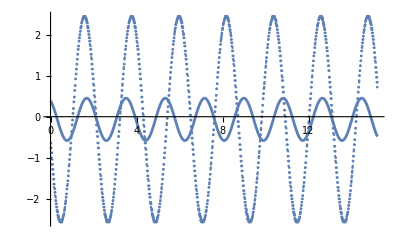

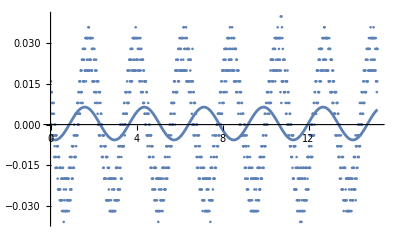

-8.43769×10^-15

-8.52651×10^-14

{{0.515428,0.0639318},{3.44011,0.027345},{2.06495,0.241283},{-0.0645547,0.0448595}}

```mathematica
dat=Import[filenms[[90]]][[5;;-1]];
dat1={#[[1]]/samplerate,#[[2]]}&/@dat[[All,1;;2]];
dat2={#[[1]]/samplerate,#[[2]]}&/@dat[[All,{1,3}]];
fit1 = NonlinearModelFit[dat1, a Sin[b t+ c] + d  , {{a,Max[dat1[[All,2]]]},{b,0.9 2 π /Max[Differences[Select[dat1,#[[2]]>0.8 Max[dat1[[All,2]]]&][[All,1]]]]},{c,2π MaximalBy[dat1,Last][[1,1]]/Max[Differences[Select[dat1,#[[2]]>0.8 Max[dat1[[All,2]]]&][[All,1]]]]-π/2},{d,0}},t];
fit2 = NonlinearModelFit[dat2, a Sin[b t+ c] + d , {{a,Max[dat2[[All,2]]]},{b,0.9 2 π /Max[Differences[Select[dat2,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]]},{c,2π MaximalBy[dat2,Last][[1,1]]/Max[Differences[Select[dat2,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]]-π/2},{d,0}},t];
Show[ListPlot[{dat2}],Plot[{fit2[t]},{t,0,dat1[[-1,1]]},PlotRange->All]]
Show[ListPlot[{dat1}],Plot[{fit1[t]},{t,0,dat1[[-1,1]]},PlotRange->All]]
Total[fit1["FitResiduals"]]
Total[fit2["FitResiduals"]]
Transpose[{fit2["BestFitParameters"][[All,2]],fit2["ParameterErrors"]}]
```

```mathematica
{}
```

{{0.515428,0.0639318},{0.0344011,0.00027345},{2.06495,0.241283},{-0.0645547,0.0448595}}

{{0.0382655,0.000214789,0.942532,0.0014807,0.537991,0.0126472,0.000196018,0.000159917,-2.49377,0.000799866,0.942443,0.000064447,2.25649,0.000576039,-0.0630178,0.000551623},{0.040389,0.000220246,0.974534,0.00135678,0.281526,0.011606,0.000334305,0.0001601,-2.49412,0.000807916,0.973882,0.0000672509,2.0177,0.000598434,-0.0624431,0.000562253},{-0.0425379,0.000223912,1.00498,0.0012315,15.7405,0.0105747,0.000417703,0.000159683,2.49318,0.00080909,1.00534,0.0000709495,4.91636,0.000627197,-0.0616413,0.000570364},{0.0447688,0.000221218,1.03679,0.00109189,6.0575,0.00943924,0.000285646,0.000155655,2.49268,0.00081552,1.03672,0.0000759676,4.67712,0.00066643,-0.0627916,0.000583499},{0.0472382,0.000234221,1.06836,0.00105223,-0.481998,0.00917389,0.000405441,0.000163749,2.49471,0.000797477,1.06813,0.0000784993,4.43833,0.000683921,-0.0619586,0.00057861},{-0.0498118,0.000223815,1.09952,0.00093594,2.40484,0.00823107,0.000419757,0.000156444,2.49397,0.000806696,1.09959,0.0000825374,4.19847,0.000715791,-0.0627184,0.000590695},{0.052534,0.000226553,1.13066,0.000901826,17.8576,0.0079916,0.000263389,0.000159135,2.49407,0.000818853,1.13094,0.0000847035,3.9591,0.00073339,-0.0622929,0.000600264},{0.0554192,0.000227555,1.16263,0.000880613,17.5913,0.00784687,0.000364454,0.000161304,2.49356,0.000844047,1.16235,0.0000857762,3.72048,0.000743815,-0.062103,0.000614232},{-0.0584335,0.000234826,1.1938,0.00089577,1.62281,0.00800105,0.000388644,0.000168318,2.49336,0.000883016,1.19382,0.0000862162,3.48158,0.000750794,-0.0622166,0.000634402},{0.0615046,0.000224996,1.22554,0.000851862,10.7788,0.00760194,0.000423826,0.000163081,-2.49256,0.000944614,1.2252,0.0000877302,6.38305,0.00076835,-0.0629384,0.000669204},{0.065052,0.00022347,1.25644,0.000829333,4.23336,0.00736823,0.00029022,0.000163254,-2.49247,0.000989682,1.25659,0.0000875435,6.14171,0.000771335,-0.0637181,0.000692861},{0.0686845,0.000225405,1.28811,0.00080939,3.96218,0.0071355,0.000283796,0.000165101,-2.49297,0.00104036,1.28811,0.0000885915,5.90452,0.000784847,-0.064036,0.000722612},{0.0723782,0.000224203,1.31957,0.000765234,3.68879,0.00667913,0.000343639,0.000163658,-2.49126,0.00108742,1.31942,0.0000908018,5.66583,0.000806974,-0.0630452,0.000752863},{0.0765086,0.000227904,1.35063,0.000724588,3.41163,0.00625788,0.000385353,0.000165077,-2.49124,0.00112489,1.35088,0.0000939032,5.42348,0.00083497,-0.0625762,0.000779811},{-0.0806107,0.000223324,1.38244,0.000657429,12.5516,0.00562417,0.000325359,0.000160296,2.48979,0.00113561,1.38227,0.0000966708,8.32544,0.000857741,-0.0606547,0.000791461},{-0.0850729,0.000226054,1.4137,0.000614958,5.98929,0.0052324,0.000376917,0.000161023,2.48929,0.00113916,1.4137,0.000100365,8.08934,0.00088653,-0.062556,0.000800789},{0.0894566,0.000227096,1.44511,0.000575966,21.4031,0.00490045,0.000383028,0.000160971,2.48786,0.00114461,1.44513,0.000105267,1.56293,0.000925104,-0.0621278,0.000813106},{0.093944,0.000229014,1.47664,0.000547927,8.54278,0.00469083,0.000328251,0.000162086,2.48674,0.00113451,1.47657,0.000108798,1.3245,0.000951104,-0.0617701,0.000814311},{0.0984636,0.000223148,1.50799,0.000510657,8.24416,0.00441981,0.000365211,0.000158201,2.4852,0.00113479,1.50797,0.000112304,1.08687,0.000977832,-0.0630229,0.000820715},{0.10296,0.000227196,1.53964,0.000503129,14.221,0.004413,0.000286183,0.000161679,2.48408,0.00115761,1.53936,0.000116092,0.84865,0.0010089,-0.062426,0.000839323},{0.106872,0.000230021,1.57073,0.000498109,1.34299,0.00442251,0.000330265,0.000164317,2.48014,0.0011605,1.57082,0.000115641,0.606751,0.00100538,-0.0619133,0.0008386},{-0.110781,0.000229925,1.6024,0.000483961,16.7311,0.00433573,0.000295795,0.000164425,2.4815,0.00116572,1.6021,0.00011317,0.36557,0.000986249,-0.0624886,0.000835739},{0.11355,0.000228751,1.63375,0.000466434,0.70298,0.00419551,0.000371394,0.000163041,2.47891,0.0011875,1.63363,0.000111309,0.125658,0.00097399,-0.0604833,0.000842877},{0.11581,0.000230038,1.66506,0.000450299,0.382171,0.00404686,0.000344897,0.000162838,-2.47827,0.0012231,1.66506,0.000110447,3.02997,0.000971121,-0.0616326,0.000860022},{0.1172,0.000238661,1.69658,0.000449118,0.0561392,0.0040177,0.000345164,0.000167639,-2.47692,0.00121675,1.6964,0.000106571,2.79156,0.000941085,-0.0622448,0.000849616},{-0.117377,0.000242798,1.71228,0.000450419,3.03281,0.00401702,0.000314408,0.000169984,2.47651,0.00124405,1.71212,0.000107761,12.0953,0.000953173,-0.0619946,0.000866714},{-0.117391,0.000236032,1.7278,0.000433424,9.15526,0.00385357,0.000280497,0.000164847,2.47683,0.00126927,1.72786,0.000109089,11.9767,0.000966181,-0.0629418,0.000883071},{-0.117119,0.000235705,1.74355,0.000430746,2.70518,0.00381854,0.000361533,0.000164355,-2.47673,0.00126398,1.74359,0.000108227,2.42884,0.000959261,-0.061054,0.000878989},{-0.116571,0.00024456,1.75928,0.000447805,2.54335,0.00395975,0.000349081,0.00017045,-2.47695,0.00126946,1.75928,0.000108704,2.31015,0.000963746,-0.0608714,0.000883185},{-0.116299,0.00023281,1.76564,0.000427367,8.76238,0.00377562,0.000428812,0.000162282,-2.47742,0.0012779,1.76546,0.000109531,2.26482,0.000971011,-0.0605898,0.000889424},{0.115921,0.000230127,1.772,0.000424162,24.4048,0.00374439,0.000375226,0.000160456,2.47667,0.00128033,1.77187,0.000109972,11.6393,0.000974811,-0.0618536,0.000891618},{-0.115726,0.000237709,1.77841,0.000439497,2.34492,0.00387737,0.000323621,0.00016581,2.4768,0.00128494,1.77812,0.000110625,11.5898,0.000980425,-0.0629763,0.00089544},{0.115201,0.000231865,1.78437,0.00043158,17.994,0.00380518,0.000294953,0.000161829,2.4752,0.00128635,1.78454,0.000111151,11.5438,0.000984716,-0.0617123,0.000897156},{-0.114774,0.000238843,1.79072,0.000447491,2.22077,0.00394355,0.000254754,0.000166823,-2.47643,0.00127481,1.79069,0.000110478,2.07164,0.000978407,-0.0614454,0.000889918},{0.114475,0.000227055,1.79704,0.000427971,24.1439,0.00377047,0.000276387,0.000158728,2.47663,0.0012746,1.79699,0.000110899,5.16276,0.000981771,-0.0620091,0.000890709},{0.113953,0.000232203,1.80329,0.000441474,24.0815,0.00388802,0.000272861,0.000162495,2.47658,0.00129229,1.80329,0.000112948,5.11639,0.000999336,-0.0622751,0.000904109},{0.113426,0.000227979,1.80959,0.000437475,17.7344,0.00385184,0.000327842,0.000159725,2.47717,0.00127563,1.80961,0.000112023,5.06693,0.000990628,-0.0619332,0.000893582},{0.112973,0.000231688,1.81589,0.000448676,5.10595,0.00394942,0.000282995,0.000162531,2.47663,0.00126413,1.81587,0.000111631,17.5867,0.000986486,-0.0632664,0.000886709},{0.112339,0.000223902,1.82225,0.000438501,5.04246,0.00385918,0.00034472,0.000157288,-2.47659,0.00128026,1.82211,0.0001137,26.9642,0.00100407,-0.0633014,0.000899293},{0.111646,0.00023374,1.82854,0.000463348,4.97659,0.00407798,0.000297249,0.000164441,2.47804,0.00128429,1.82832,0.000114672,4.92571,0.00101192,-0.0608343,0.000903465},{0.11109,0.000233632,1.83435,0.000468142,4.91863,0.00411982,0.000338592,0.0001646,2.4779,0.00127811,1.83466,0.000114852,4.87763,0.00101271,-0.0620987,0.00090053},{-0.110377,0.000228867,1.84087,0.000464666,26.8453,0.00408881,0.000288806,0.000161512,2.47882,0.00127805,1.84089,0.000115546,4.83017,0.00101801,-0.0629703,0.000901933},{0.109728,0.00023266,1.8473,0.0004784,4.78977,0.00420949,0.000249483,0.000164466,2.47713,0.00129309,1.84737,0.000117788,11.0653,0.00103681,-0.0630119,0.000914096},{0.109122,0.000224057,1.85358,0.000466399,4.72395,0.00410434,0.000330602,0.00015865,2.47869,0.0012756,1.85349,0.000116886,4.73335,0.00102814,-0.0616253,0.000903204},{0.108284,0.000231595,1.85993,0.000489145,17.2287,0.0043038,0.000309497,0.000164268,2.47781,0.00128731,1.8598,0.000118804,4.68541,0.00104411,-0.0609522,0.000913035},{0.10768,0.000229625,1.86616,0.000490952,4.60247,0.00431876,0.000337374,0.000163141,2.47811,0.00127195,1.86615,0.000118172,4.63849,0.00103759,-0.0626776,0.000903673},{0.106868,0.000226815,1.87246,0.000491842,4.53935,0.00432606,0.000189617,0.00016141,2.47907,0.00129492,1.87235,0.000121051,4.59207,0.00106194,-0.063907,0.000921503},{0.106045,0.000229762,1.87875,0.000505279,4.47671,0.00444343,0.000318921,0.000163767,2.47845,0.00128332,1.87871,0.000120786,4.54167,0.00105883,-0.0629383,0.000914748},{-0.105333,0.000222844,1.88507,0.000496389,26.4079,0.00436356,0.000225004,0.000159079,2.47936,0.00127641,1.88497,0.000120843,4.49595,0.00105838,-0.0627371,0.000911241},{0.104479,0.000225388,1.89105,0.000508893,4.35747,0.00447212,0.000391414,0.000161114,2.47877,0.00128108,1.89117,0.000122033,4.44713,0.00106807,-0.0622945,0.000915933},{-0.103754,0.000221742,1.89748,0.00050688,26.2859,0.00445246,0.000333597,0.000158723,2.47952,0.00129657,1.8975,0.000124177,4.39922,0.00108601,-0.062902,0.000928328},{0.102785,0.0002177,1.90377,0.000504746,16.8002,0.00443141,0.000360359,0.000156018,2.4806,0.00127653,1.90381,0.000122853,4.35178,0.00107365,-0.0628971,0.000915185},{0.102006,0.000223046,1.90993,0.000523292,10.4587,0.00459135,0.000259036,0.000160017,2.48089,0.0012717,1.91004,0.000122963,4.30456,0.00107391,-0.0629665,0.000912803},{0.101135,0.000221652,1.91661,0.000526499,10.3913,0.00461665,0.000304237,0.000159167,2.48094,0.00129069,1.91631,0.000125336,4.25433,0.00109407,-0.0626896,0.00092741},{0.100411,0.000225335,1.92274,0.00054081,10.3363,0.00473807,0.000236411,0.000161936,2.48119,0.00128266,1.92268,0.000125027,4.20786,0.00109071,-0.0622365,0.000922498},{0.0994852,0.000226012,1.92907,0.000548809,3.9911,0.00480434,0.000268699,0.000162517,2.48184,0.00128708,1.92892,0.00012583,4.15967,0.00109721,-0.0610572,0.00092638},{0.0986732,0.000222646,1.93517,0.00054611,3.93459,0.00477638,0.000284507,0.000160166,2.4815,0.00128975,1.93517,0.000126442,4.11488,0.00110205,-0.0626994,0.000928851},{0.0978878,0.000222431,1.94154,0.000550588,3.87241,0.00481105,0.00032523,0.000160049,2.48251,0.00129704,1.94143,0.000127359,4.06337,0.00110973,-0.0639267,0.00093449},{0.096965,0.000228254,1.94751,0.000570691,3.81559,0.00498196,0.00018415,0.000164252,2.48286,0.00130969,1.94773,0.000128763,4.01646,0.00112164,-0.0638116,0.000943841},{0.0216579,0.00244111,2.54182,0.0247403,2.43503,0.217297,-0.00102898,0.00171069,2.4816,0.00131402,1.96347,0.000129329,3.89551,0.00112617,-0.0626126,0.000946779},{0.0207159,0.00238755,2.55719,0.0252305,2.27421,0.221976,-0.000864635,0.00167251,2.48335,0.0013092,1.97919,0.000128321,3.77639,0.00111752,-0.0628703,0.000942087},{-0.0905009,0.000219694,1.99476,0.000581013,12.8018,0.00503156,0.000357534,0.00015748,0.538907,0.0641053,2.56988,0.0258081,2.42635,0.228028,-0.0667314,0.0448025},{-0.0883576,0.000221076,2.01045,0.000593246,6.37389,0.00512613,0.000392083,0.000158067,-2.48522,0.00137188,2.01062,0.000132025,6.67815,0.00115155,-0.0632655,0.000981932},{0.0840528,0.000223766,2.04221,0.000617502,28.081,0.00532346,0.000301543,0.000159076,-2.48622,0.00140946,2.0421,0.000131929,6.43928,0.0011542,-0.0620878,0.00100125},{-0.080018,0.00022775,2.07352,0.000646271,5.8099,0.00557814,0.00035203,0.000161064,-2.48714,0.00148316,2.07343,0.00013465,6.19921,0.00118231,-0.0627121,0.00104557},{0.0762513,0.000230751,2.10499,0.000675747,33.8096,0.00586232,0.000331447,0.000162551,-2.48947,0.00153697,2.10482,0.000135755,5.96005,0.00119637,-0.0621911,0.00107682},{0.0725549,0.000229516,2.13636,0.000699677,20.9745,0.00611846,0.000319773,0.000161346,-0.489768,0.0613265,2.7392,0.0295861,4.27545,0.258811,-0.0598467,0.0438033},{0.0691505,0.000229359,2.16728,0.000732472,8.14704,0.00646269,0.000241527,0.000161207,2.49141,0.00162335,2.16765,0.000140002,8.62442,0.00123884,-0.062286,0.00113231},{-0.0658148,0.00023042,2.1991,0.000777903,4.73463,0.00692032,0.000228294,0.000162215,2.49222,0.00164808,2.19907,0.000143132,8.38167,0.00126606,-0.062705,0.00115207},{0.0626217,0.000224764,2.23046,0.0008057,13.9013,0.00720673,0.000247197,0.000158635,2.49329,0.00165282,2.23058,0.000146151,8.14264,0.00129018,-0.0601745,0.00116082},{0.0597506,0.000226194,2.2617,0.000860019,1.07433,0.00770534,0.000369806,0.000160118,2.4941,0.00164372,2.26191,0.00014905,1.61857,0.00131186,-0.0620779,0.00116178},{0.0569984,0.000224925,2.29366,0.000906097,7.09916,0.00809614,0.000293355,0.000159648,2.49441,0.0016495,2.2933,0.000153676,1.37902,0.00134792,-0.0628696,0.0011738},{0.0544558,0.000227349,2.32476,0.000966059,19.421,0.00857621,0.000312516,0.000161693,2.49523,0.00165327,2.3248,0.00015753,1.14415,0.00137721,-0.0640982,0.0011832},{0.0520511,0.000228651,2.35629,0.00101993,0.316497,0.0089746,0.00025739,0.000162778,2.49689,0.00166524,2.35609,0.000160623,0.903525,0.00140146,-0.0630487,0.0011954},{-0.0497002,0.000224138,2.38838,0.00104683,22.0512,0.00912277,0.000353412,0.000159574,2.49761,0.00168083,2.38764,0.000162104,0.660716,0.00141347,-0.0626375,0.00120607},{0.0475542,0.000221137,2.41902,0.00107653,-0.177099,0.00930905,0.000471884,0.000157337,0.533429,0.0641363,2.99668,0.0262508,-0.827647,0.231783,-0.0616779,0.0448937},{-0.0455023,0.000224385,2.45022,0.00113525,9.00235,0.0097719,0.000260641,0.000159419,-2.49832,0.00171761,2.45046,0.000160117,-2.9572,0.00140054,-0.0609898,0.0012207},{0.0435076,0.000221789,2.48203,0.0011653,37.0275,0.0100285,0.000314007,0.000157279,-2.49919,0.00174297,2.48186,0.000158401,3.08437,0.00138958,-0.0633674,0.00123078},{-0.0417696,0.000218553,2.51287,0.00118775,2.23266,0.0102643,0.000261254,0.000154689,-2.50104,0.00171225,2.51329,0.000151935,2.84318,0.00133701,-0.0625117,0.00120242},{-0.0399938,0.00021989,2.5446,0.0012407,8.27406,0.0108043,0.000329379,0.000155379,-2.49995,0.00178574,2.54469,0.000155943,2.60676,0.00137597,-0.062393,0.00124949},{-0.0383729,0.000222897,2.5755,0.00130707,1.75393,0.0114837,0.000376137,0.00015737,-2.50142,0.00179933,2.57613,0.000156003,2.36673,0.00137853,-0.0606152,0.00125752},{-0.0034597,0.000975984,1.16214,0.0640474,9.12888,0.5484,-0.000750548,0.000699692,2.50099,0.00179975,2.60754,0.000156738,5.26657,0.00138514,-0.0615888,0.00125953},{0.0354792,0.000215792,2.63833,0.00137423,4.41767,0.0122514,0.000338959,0.000152475,2.50082,0.00180167,2.63893,0.000159137,5.0269,0.00140451,-0.0632142,0.00126542},{0.0340385,0.00022007,2.67015,0.00146904,16.7481,0.0131301,0.000241761,0.000155707,2.50245,0.00182007,2.67029,0.000164032,4.79049,0.00144414,-0.063733,0.00128498},{0.0327349,0.000221908,2.70099,0.00155028,35.3688,0.0138359,0.000300775,0.000157262,2.50217,0.00180628,2.7018,0.000166626,4.55071,0.00146268,-0.0620963,0.00128265},{0.0313626,0.000215649,2.73266,0.00158216,16.2837,0.0140486,0.000245761,0.000153071,2.50275,0.00181334,2.73311,0.000170644,4.31026,0.00149387,-0.0619225,0.00129417},{-0.0303159,0.000217559,2.76491,0.00165836,19.1831,0.0146122,0.000310589,0.000154606,2.50373,0.00181983,2.7646,0.000173371,4.06772,0.00151464,-0.0617528,0.0013028},{0.0289993,0.000222766,2.79581,0.00177881,9.53237,0.0155454,0.000266451,0.000158398,2.50377,0.00185421,2.79608,0.000177023,3.83089,0.00154507,-0.0598207,0.00132772},{0.000136506,0.000752202,282.99,1.25789,531.199,11.0313,-5.29855×10^-6,0.000532105,2.50424,0.00188457,2.82744,0.000178337,3.59398,0.00155725,-0.0628162,0.00134593},{0.00607162,0.000707093,2.2679,0.0265092,29.3779,0.237094,0.000394614,0.000500765,0.515428,0.0639318,3.44011,0.027345,2.06495,0.241283,-0.0645547,0.0448595},{-0.00280507,0.000697306,1.44907,0.0570971,1.22489,0.511203,0.000459368,0.000496094,-0.499434,0.0634732,3.47599,0.0284095,4.93784,0.250333,-0.0614941,0.0446939},{-0.00252265,0.000671598,1.47036,0.0624292,7.30937,0.557168,0.00059891,0.000480338,-2.50464,0.00208368,2.92165,0.000185895,6.01211,0.00163416,-0.0613441,0.00146579},{-0.00242408,0.000647932,1.49503,0.0636287,19.6306,0.564786,0.000596209,0.000465241,2.505,0.00211344,2.95309,0.000185632,8.91712,0.00163598,-0.0611107,0.0014815},{0.0232564,0.000228502,2.98427,0.00219578,8.17703,0.0192908,0.000199567,0.000160955,2.50569,0.00214497,2.98447,0.00018697,8.68193,0.00165041,-0.0647677,0.00150139}}

```mathematica
Differences[Select[dat2,#[[2]]>0.90 Max[dat2[[All,2]]]&][[All,1]]]
```

```mathematica
Select[dat2,#[[2]]>0.90 Max[dat2[[All,2]]]&][[All,1]]
Differences[Select[dat2,#[[2]]>0.90 Max[dat2[[All,2]]]&][[All,1]]]
```

{168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,198,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,620,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,830,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1040,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234,1235,1236,1237,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247,1248,1249,1250,1252,1432,1433,1434,1435,1436,1437,1438,1439,1440,1441,1442,1443,1444,1445,1446,1447,1448,1449,1450,1451,1452,1453,1454,1455,1456,1457,1458,1459,1460,1462}

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,180,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,180,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,180,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,180,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,180,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,180,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2}

```mathematica
D[Sin[ω t + ϕ],{t,2}]
```

-ω^2 Sin[ϕ+t ω]

```mathematica
Solve[{Cos[ϕ+t ω]==0,Sin[ϕ+t ω]<0},ϕ]
```

{{ϕ→ConditionalExpression[1/2 (-π-2 t ω+4 π C[1]), C[1]∈ℤ]},{ϕ→ConditionalExpression[1/2 (-π-2 t ω+4 π (C[1]-C[2])), (C[1]|C[2])∈ℤ&&C[1]≥0&&C[2]≥0]}}

192

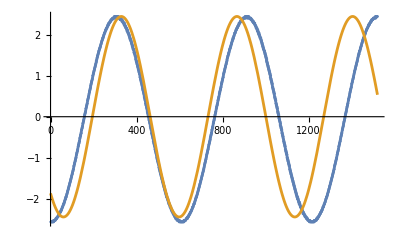

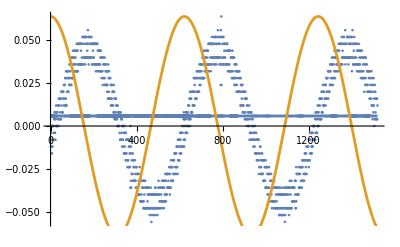

```mathematica
rl1=Evaluate[{a->Max[dat2[[All,2]]],b->0.9 2 π /Max[Differences[Select[dat2,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]],c->-2π MaximalBy[dat2,Last][[1,1]]/Max[Differences[Select[dat2,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]]+π/2,d->0}];
rl2=Evaluate[{a->Max[dat1[[All,2]]],b->0.9 2 π /Max[Differences[Select[dat1,#[[2]]>0.8 Max[dat1[[All,2]]]&][[All,1]]]],c->-2π MaximalBy[dat1,Last][[1,1]]/Max[Differences[Select[dat1,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]]+π/2,d->0}];
Show[ListPlot[{dat2}],Plot[{fit2[t],(a Sin[b t+ c] + d)/.rl1},{t,0,dat1[[-1,1]]},PlotRange->All]]
Show[ListPlot[{dat1}],Plot[{fit1[t],(a Sin[b t+ c] + d)/.rl2},{t,0,dat1[[-1,1]]},PlotRange->All]]
```

```mathematica
Max[Differences[Select[dat1,#[[2]]>0.90 Max[dat1[[All,2]]]&][[All,1]]]]
```

-∞

```mathematica
Differences[Select[dat1,#[[2]]>0.90 Max[dat1[[All,2]]]&][[All,1]]]
```

{}

```mathematica
Select[dat1,#[[2]]>0.8 Max[dat1[[All,2]]]&]
```

{{148,0.052},{152,0.052},{154,0.052},{156,0.052},{158,0.052},{162,0.052},{164,0.052},{166,0.052},{174,0.056},{176,0.052},{178,0.052},{182,0.052},{188,0.052},{190,0.052},{750,0.052},{760,0.052},{764,0.052},{766,0.052},{768,0.052},{776,0.052},{778,0.056},{780,0.052},{786,0.052},{790,0.052},{792,0.056},{794,0.064},{796,0.052},{798,0.052},{802,0.052},{804,0.052},{1354,0.052},{1362,0.052},{1364,0.052},{1370,0.056},{1378,0.052},{1380,0.052},{1382,0.052},{1384,0.052},{1388,0.052},{1394,0.052},{1398,0.052},{1402,0.052},{1404,0.056},{1412,0.052}}